```mathematica
A=RandomReal[{-5,5},{100,2}]
```

```mathematica
A={#[[1]],Sin[#[[2]]]}&/@A;
```

```mathematica
f[x0_]:=Module[{x=x0,A=A},
A=#[[1]]*x+#[[2]](1-x)&/@A;
A=Sort[A];
A[[Ceiling[0.05*Length[A]]]]
]
```

```mathematica
f[0]
```

-0.9928

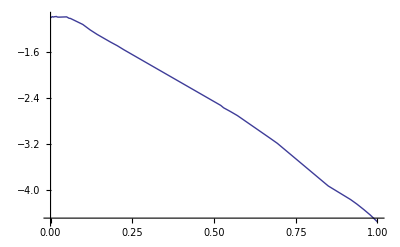

```mathematica
Plot[f[x],{x,0,1}]
```

```mathematica
Exit[]
```

```mathematica
1
```

```mathematica
Solve[mu==x*H*(a+b)+(1-x)a A+(1-x)b R-3 G-3 M,x]
```

{{x→(a A-3 G-3 M-mu+b R)/(a A-a H-b H+b R)}}

```mathematica
CForm[%[[1,1,2]]]
```

(a*A - 3*G - 3*M - mu + b*R)/(a*A - a*H - b*H + b*R)

```mathematica
2
```

```mathematica
Solve[mu==x*H*(a+b)+(1-x)a A+(1-x)b R-3 G-x t (a+b+a+b),x]
```

{{x→(a A-3 G-mu+b R)/(a A-a H-b H+b R+2 a t+2 b t)}}

```mathematica
CForm[%[[1,1,2]]]
```

(a*A - 3*G - mu + b*R)/(a*A - a*H - b*H + b*R + 2*a*t + 2*b*t)

```mathematica
3
```

```mathematica
Solve[mu==x*H*(a+b)+(1-x)a A+(1-x)b R-3 G-2 M-x a t,x]
```

{{x→(a A-3 G-2 M-mu+b R)/(a A-a H-b H+b R+a t)}}

```mathematica
CForm[%[[1,1,2]]]
```

(a*A - 3*G - 2*M - mu + b*R)/(a*A - a*H - b*H + b*R + a*t)

```mathematica
4
```

```mathematica
Solve[mu==x*H*(a+b)+(1-x)a A+(1-x)b R-3 G-M-x t(a+b),x]
```

{{x→(a A-3 G-M-mu+b R)/(a A-a H-b H+b R+a t+b t)}}

```mathematica
CForm[%[[1,1,2]]]
```

(a*A - 3*G - M - mu + b*R)/(a*A - a*H - b*H + b*R + a*t + b*t)

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→0.896996}}

```mathematica
f[x_]:=x*H*(a+b)+(1-x)a A+(1-x)b R-3 G-Min[M,x (a+b)t];
Reduce[mu==f[x]&&0<x<1&&a<b&&a>0&&b>0,x]
```

$Aborted

```mathematica
Exit[]
```

```mathematica
CForm[f[x]]
```

-3*G + (a + b + c)*(A*e*(1 - x) + (1 - e)*R*(1 - x) + H*x) - 
   Min(M,(a + b + c)*t*x) - Min(M,
    Abs(t*(b - (a + b + c)*(1 - e)*(1 - x)))) - 
   Min(M,t*Abs(a - (a + b + c)*e*(1 - x)))

```mathematica
Exit[]
```

```mathematica
f[x_]:=(a+b+c)(x*H+(1-x)e A+(1-x)(1-e) R)-3 G-Min[M,x (a+b+c)t]-Min[M, t Abs[a-(1-x)e (a+b+c)]]- Min[M , Abs[t (b-(1-x)(1-e) (a+b+c))]];
S=Solve[mu==f[x],x];Flatten[{#[[2]]}&/@Transpose[S][[1]]]
```

$Aborted

```mathematica
Union[AA1,AA2]
```

```mathematica
CForm[%]
```

```mathematica
mu=2;H=3;A=1.1;R=10.10;a=5;b=3;c=0.1;e=0.9;M=10;G=8;t=9;
f[x_]:=(a+b+c)(x*H+(1-x)e A+(1-x)(1-e) R)-3 G-Min[M,x (a+b+c)t]-Min[M, t Abs[a-(1-x)e (a+b+c)]]- Min[M , Abs[t (b-(1-x)(1-e) (a+b+c))]];
```

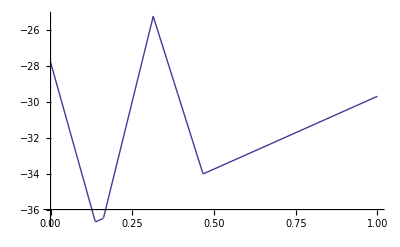

```mathematica
Plot[f[x],{x,0.0,1},PlotRange->All]
```

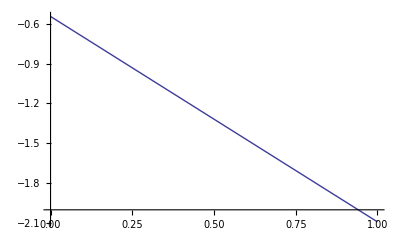

```mathematica
Plot[((x*H+(1-x)a/(a+b) A+(1-x)b/(a+b)R)(a+b)-3 G-3 M)/(a+b),{x,0,1}]
```

```mathematica
CForm[x*H*(a+b)+(1-x)a A+(1-x)b R-3 G-Min[M,x (a+b)t]-Min[M,x a t]-Min[M,x b t]]
```

-3*G + a*A*(1 - x) + b*R*(1 - x) + (a + b)*H*x - Min(M,a*t*x) - 
   Min(M,b*t*x) - Min(M,(a + b)*t*x)

```mathematica
Exit[]
```

```mathematica
Simplify[Solve[(a A-3 G-mu+b R)/(a A-a H-b H+b R+2 a t+2 b t)==(a A-3 G-M-mu+b R)/(a A-a H-b H+b R+a t+b t),mu][[1,1,2]]]
```

(a^2 A t+a (-A M+H M+A b t-3 G t-2 M t+b R t)+b (H M-3 G t+b R t-M (R+2 t)))/((a+b) t)

```mathematica
CForm[%]
```

(Power(a,2)*A*t + a*(-(A*M) + H*M + A*b*t - 3*G*t - 2*M*t + b*R*t) + 
     b*(H*M - 3*G*t + b*R*t - M*(R + 2*t)))/((a + b)*t)